# Nelson Siegel

## Definition

```mathematica
ShortLoading[t_,tau_]:=If[t==0,1,(1-Exp[-t/tau])/(t/tau)];
MediumLoading[t_,tau_]:=ShortLoading[t,tau]-Exp[-t/tau];
NelsonSiegel[t_,rlong_,rshort_,rmedium_,tau_]:=rlong+rshort*ShortLoading[t,tau]+rmedium*MediumLoading[t,tau]
```

## Example

```mathematica
rlong =0.08;
rshort=0.01;
rmedium=0.0;
tau=5;
```

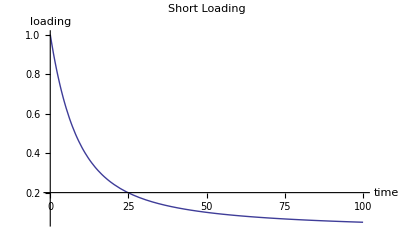

```mathematica
Plot[ShortLoading[t,tau],{t,0,100},PlotLabel->"Short Loading",AxesLabel->{"time","loading"},PlotRange->All]
```

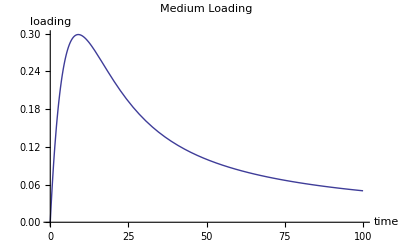

```mathematica
Plot[MediumLoading[t,tau],{t,0,100},PlotLabel->"Medium Loading",AxesLabel->{"time","loading"},PlotRange->All]
```

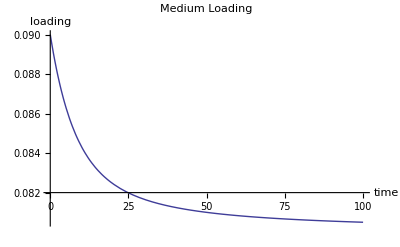

```mathematica
Plot[NelsonSiegel[t,rlong,rshort,rmedium,tau],{t,0,100},PlotLabel->"Medium Loading",AxesLabel->{"time","loading"},PlotRange->All]
```